Cadenas de caracteres y texto

Wolfram Language también permite efectuar procesos de cómputo con texto. El texto se introduce como una cadena de caracteres, demarcada por comillas (").

Introducir una cadena de caracteres:

```mathematica
"This is a string."
```

This is a string.

Al igual que cuando se ingresa un número, al introducir una cadena tal cual, no se genera ningún cambio, salvo que las comillas no son visibles cuando se muestra el resultado. Hay muchas funciones que trabajan con cadenas, como StringLength, que produce la longitud de una cadena.

StringLength cuenta el número de caracteres en una cadena:

```mathematica
StringLength["hello"]
```

5

StringReverse invierte el orden de los caracteres que componen una cadena:

```mathematica
StringReverse["hello"]
```

olleh

ToUpperCase pone en mayúsculas todos los caracteres de una cadena:

```mathematica
ToUpperCase["I'm coding in the Wolfram Language!"]
```

I'M CODING IN THE WOLFRAM LANGUAGE!

StringTake toma un número dado de los caracteres de una cadena, a partir del primero:

```mathematica
StringTake["this is about strings",10]
```

this is ab

Si se toman 10 caracteres se obtiene una cadena de longitud 10:

```mathematica
StringLength[StringTake["this is about strings",10]]
```

10

StringJoin junta cadenas (no hay que olvidar los espacios si se desea separar palabras):

```mathematica
StringJoin["Hello"," ", "there!", " How are you?"]
```

Hello there! How are you?

Se pueden formar listas de cadenas y luego aplicarle alguna función al resultado.

Una lista de cadenas:

```mathematica
{"apple","banana","strawberry"}
```

{apple,banana,strawberry}

Obtenga los dos primeros caracteres de cada cadena:

```mathematica
StringTake[{"apple","banana","strawberry"},2]
```

{ap,ba,st}

StringJoin junta las cadenas de una lista dada:

```mathematica
StringJoin[{"apple","banana","strawberry"}]
```

applebananastrawberry

Es útil poder convertir cadenas en listas de los caracteres que las forman. Cada uno de los caracteres resultantes es, en sí mismo, una cadena de longitud 1.

Characters descompone una cadena en una lista de sus caracteres:

```mathematica
Characters["a string is made of characters"]
```

{a, ,s,t,r,i,n,g, ,i,s, ,m,a,d,e, ,o,f, ,c,h,a,r,a,c,t,e,r,s}

Una vez que se ha descompuesto una cadena en una lista de caracteres, pueden usarse con ella todas las operaciones usuales de listas.

Ordene los caracteres de una cadena:

```mathematica
Sort[Characters["a string of characters"]]
```

{ , , ,a,a,a,c,c,e,f,g,h,i,n,o,r,r,r,s,s,t,t}

Los elementos invisibles al principio de la lista son espaciadores. En caso de que se desee ver las cadenas en la forma como se habrían digitado, incluyendo "...", hay que usar InputForm.

InputForm muestra las cadenas en la forma como se digitarían, incluyendo las comillas:

```mathematica
InputForm[Sort[Characters["a string of characters"]]]
```

{" ", " ", " ", "a", "a", "a", "c", "c", "e", "f", "g", "h", "i", "n", "o", "r", 
 "r", "r", "s", "s", "t", "t"}

Las funciones como StringJoin y Characters operan sobre cadenas de todo tipo, sin importar que tengan algún significado. Otras funciones, tales como TextWords, trabajan específicamente con texto que tenga algún sentido, es decir, que esté escrito en inglés, por ejemplo.

TextWords produce la lista de las palabras en una cadena de texto dado:

```mathematica
TextWords["This is a sentence. Sentences are made of words."]
```

{This,is,a,sentence,Sentences,are,made,of,words}

Lo siguiente dará la longitud de cada palabra:

```mathematica
StringLength[TextWords["This is a sentence. Sentences are made of words."]]
```

{4,2,1,8,9,3,4,2,5}

TextSentences descompone una cadena de texto en una lista de frases:

```mathematica
TextSentences["This is a sentence. Sentences are made of words."]
```

{This is a sentence.,Sentences are made of words.}

Existen muchas formas de obtener texto en Wolfram Language. Por ejemplo, la función WikipediaData obtiene el texto actual de algún artículo de Wikipedia.

Obtenga los 100 primeros caracteres del artículo de Wikipedia sobre computadoras o computers en inglés:

```mathematica
StringTake[WikipediaData["computers"],100]
```

A computer is a general-purpose device that can be programmed to carry out a set of arithmetic or lo

Una buena forma de hacerse una idea de lo que contiene un texto es formando una nube de palabras. Esto se logra con la función WordCloud.

Cree una nube de palabras con el artículo de Wikipedia sobre computadoras o “computers” en inglés:

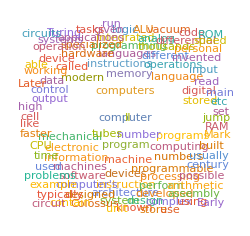

```mathematica
WordCloud[WikipediaData["computers"]]
```

Como sería de esperar, computer y computers son las palabras más comunes en ese artículo.

Wolfram Language contiene mucha información intrínseca sobre palabras del inglés y de otras lenguas. WordList obtiene listas de palabras.

Obtenga las 20 primeras palabras de una lista de palabras comunes del inglés:

```mathematica
Take[WordList[ ],20]
```

{a,aah,aardvark,aback,abacus,abaft,abalone,abandon,abandoned,abandonment,abase,abasement,abash,abashed,abashment,abate,abatement,abattoir,abbe,abbess}

Cree una nube de palabras a partir de las letras iniciales de todas las palabras:

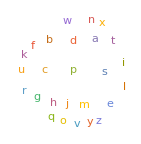

```mathematica
WordCloud[StringTake[WordList[ ],1]]
```

Las cadenas no necesariamente tienen que contener texto. En una yuxtaposición de un sistema antiguo con moderno se puede generar, por ejemplo, los números romanos como cadenas.

Genere la cadena del número romano para 1988

```mathematica
RomanNumeral[1988]
```

MCMLXXXVIII

Cree una tabla de los números romanos para los enteros del 1 al 20:

```mathematica
Table[RomanNumeral[n],{n,20}]
```

{I,II,III,IV,V,VI,VII,VIII,IX,X,XI,XII,XIII,XIV,XV,XVI,XVII,XVIII,XIX,XX}

Como para todo lo demás, pueden hacerse cálculos con estas cadenas. Por ejemplo, pueden graficarse las longitudes de los números romanos consecutivos.

Presente gráficamente las longitudes de los símbolos para los números romanos de los enteros del 1 al 100:

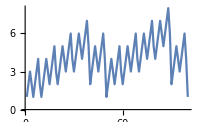

```mathematica
ListLinePlot[Table[StringLength[RomanNumeral[n]],{n,100}]]
```

IntegerName da el nombre en inglés de un entero.

Genere una cadena con el nombre en inglés del entero 56:

```mathematica
IntegerName[56]
```

fifty-six

A continuación se tiene una presentación gráfica de las longitudes de los nombres de los números en inglés:

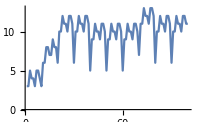

```mathematica
ListLinePlot[Table[StringLength[IntegerName[n]],{n,100}]]
```

Hay muchas formas de convertir letras en números (y viceversa).

Alphabet produce el alfabeto del inglés:

```mathematica
Alphabet[ ]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

LetterNumber dice en qué posición del alfabeto inglés aparece una letra dada:

```mathematica
LetterNumber[{"a","b","x","y","z"}]
```

{1,2,24,25,26}

FromLetterNumber hace lo contrario de lo anterior:

```mathematica
FromLetterNumber[{10,11,12,13,14,15}]
```

{j,k,l,m,n,o}

Alphabet también conoce alfabetos de otras lenguas, aparte del inglés:

```mathematica
Alphabet["Russian"]
```

{а,б,в,г,д,е,ё,ж,з,и,й,к,л,м,н,о,п,р,с,т,у,ф,х,ц,ч,ш,щ,ъ,ы,ь,э,ю,я}

Transliterate convierte (aproximadamente) a las letras equivalentes en inglés:

```mathematica
Transliterate[Alphabet["Russian"]]
```

{a,b,v,g,d,e,e,z,z,i,j,k,l,m,n,o,p,r,s,t,u,f,h,c,c,s,s,ʺ,y,ʹ,e,u,a}

Con esto se translitera la palabra “wolfram” al alfabeto ruso:

```mathematica
Transliterate["wolfram","Russian"]
```

уолфрам

Si se quiere, se puede convertir texto en imágenes, las cuales pueden manipularse mediante procesamiento de imágenes. La función Rasterize produce un raster, o bitmap, de alguna cosa.

Genere la imagen de una porción de texto:

```mathematica
Rasterize[Style["ABC",100]]
```

-Graphics-

Efectúe procesamiento de imágenes con el resultado:

```mathematica
EdgeDetect[Rasterize[Style["ABC",100]]]
```

-Graphics-

Vocabulario

"cadena" |   | una cadena de caracteres
StringLength["string"] |   | longitud de una cadena
StringReverse["string"] |   | invierte una cadena 
StringTake["string",4] |   | toma caracteres a partir del principio de una cadena 
StringJoin["string","string"] |   | junta cadenas 
StringJoin[{"string","string"}] |   | junta una lista de cadenas
ToUpperCase["string"] |   | convierte caracteres a mayúsculas 
Characters["string"] |   | convierte una cadena en una lista de caracteres 
TextWords["string"] |   | lista de las palabras en una cadena 
TextSentences["string"] |   | lista de las frases 
WikipediaData["tema"] |   | artículo de Wikipedia sobre un tema
WordCloud["text"] |   | nube de palabras a partir de las frecuencias de palabras 
WordList[ ] |   | lista de palabras comunes del inglés 
Alphabet[ ] |   | lista de las letras del alfabeto inglés
LetterNumber["c"] |   | en qué posición del alfabeto inglés aparece una letra 
FromLetterNumber[n] |   | la letra que aparece en una posición dada del alfabeto inglés
Transliterate["text"] |   | translitera texto de cualquier lengua al inglés
Transliterate["text","alphabet"] |   | translitera texto a otros alfabetos
RomanNumeral[n] |   | convierte un número en la cadena de su equivalente romano
IntegerName[n] |   | convierte un número a la cadena de su nombre en inglés
InputForm["string"] |   | muestra una cadena con comillas 
Rasterize["string"] |   | hace una imagen en bitmap

"30 Exercises Available"
"with 13 extras" | "Get Started »"

Junte dos copias de la cadena "Hello". »

| Expected output: |  
  | "HelloHello" |

Forme una sola cadena con el alfabeto inglés con los caracteres en mayúscula. »

| Expected output: |  
  | "ABCDEFGHIJKLMNOPQRSTUVWXYZ" |

Genere una cadena con el alfabeto inglés en orden inverso. »

| Expected output: |  
  | "zyxwvutsrqponmlkjihgfedcba" |

Junte 100 copias de la cadena "AGCT". »

| Expected output: |  
  | "AGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCTAGCT" |

Use StringTake, StringJoin y Alphabet para obtener "abcdef". »

| Expected output: |  
  | "abcdef" |

Forme una columna con números crecientes consecutivos de las letras de la cadena "this is about strings". »

| Expected output: |  
  | "t"
"th"
"thi"
"this"
"this "
"this i"
"this is"
"this is "
"this is a"
"this is ab"
"this is abo"
"this is abou"
"this is about"
"this is about "
"this is about s"
"this is about st"
"this is about str"
"this is about stri"
"this is about strin"
"this is about string"
"this is about strings" |

Haga un diagrama de barras con las longitudes de las palabras en “A long time ago, in a galaxy far, far away”. »

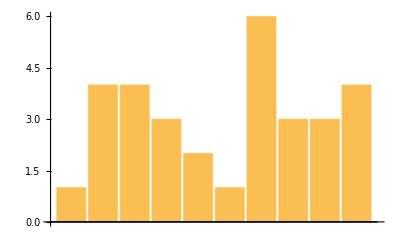
| Expected output: |  
  | -Graphics- |

Encuentre la longitud de la cadena formada con los caracteres en el artículo de Wikipedia “computer”. »

| Sample expected output: |  
  | 49848 |

Cuente cuántas palabras hay en el artículo de Wikipedia “computer”. »

| Sample expected output: |  
  | 7742 |

Encuentre la primera frase en el artículo de Wikipedia “strings”. »

| Sample expected output: |  
  | "String is a flexible piece of rope or twine which is used to tie, bind, or hang other objects." |

Forme una cadena con los caracteres iniciales en todas la frases que hay en el artículo de Wikipedia sobre computadoras. »

| Sample expected output: |  
  | "ASCTPMIDOMCPH="ITFTLTTTSITIIDMTTAAATTTIAATAIBIATITIITS=CATFTTTAEBNH=HTTTLHTWAB=THHHVTE=TDETTITPIRT=TEIBTDTTHACIINCTAILOIIIHBTCWATIHJTIWIAATBAITFCSTATHT=TDTKINHPTWTTTMIALITHTFMPWSTCBOTI=TTSTTITMWITCUTTS=FTHHIT=TEALTP=TBOBSA=TIET=CATDIRTPIWJSAITETSHTALATSGETTLSIETWOAMTTRACRIIISFIIGDOHCIAMTOBItSTBSITMSTSS=TITTITCIIA"QCSLTTT=W"A=HFMMH=C=C=W=T=TTSOSCT=" |

Encuentre la mayor longitud de palabra entre todas las palabras del inglés encontradas en WordList[ ]. »

| Sample expected output: |  
  | 23 |

Cuente el número de palabras en WordList[ ] que comienzan con “q”. »

| Sample expected output: |  
  | 197 |

Presente la gráfica, con los puntos unidos, de las longitudes de las 1000 primeras palabras de WordList[ ]. »

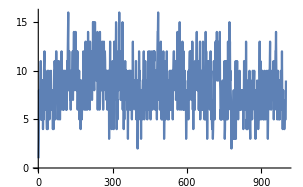
| Sample expected output: |  
  | -Graphics- |

Use StringJoin y Characters para formar la nube de palabras en todas las palabras obtenidas de WordList[ ]. »

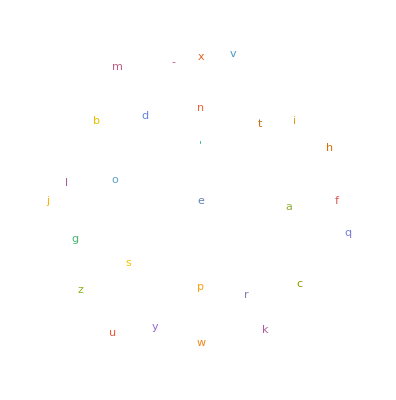
| Sample expected output: |  
  | -Graphics- |

Use StringReverse para hacer la nube de palabras de las letras finales en cada palabra obtenida de WordList[ ]. »

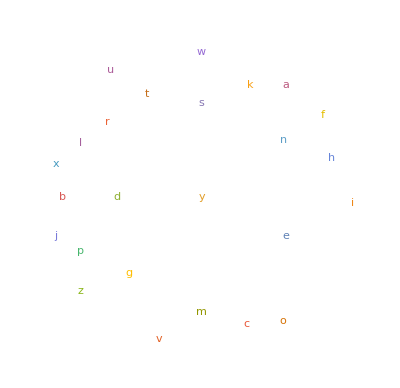
| Sample expected output: |  
  | -Graphics- |

Encuentre el número romano correspondiente al año 1959. »

| Expected output: |  
  | "MCMLIX" |

Encuentre la mayor longitud de cadena entre los números romanos para los años del 1 al 2020. »

| Expected output: |  
  | 13 |

Cree una nube de palabras con los caracteres iniciales de cada uno de los números romanos del 1 al 100. »

| Expected output: |  
  |  |

Use Length para encontrar la longitud del alfabeto ruso. »

| Expected output: |  
  | 33 |

Genere las mayúsculas del alfabeto griego. »

| Expected output: |  
  | {"Α","Β","Γ","Δ","Ε","Ζ","Η","Θ","Ι","Κ","Λ","Μ","Ν","Ξ","Ο","Π","Ρ","Σ","Τ","Υ","Φ","Χ","Ψ","Ω"} |

Cree un diagrama de barras de los números de letra en la palabra “wolfram”. »

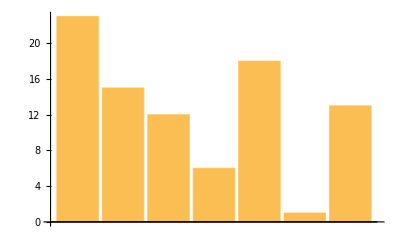
| Expected output: |  
  | -Graphics- |

Use FromLetterNumber para hacer una cadena de 1000 letras al azar. »

| Sample expected output: |  
  | "chfpmqpcyncvrvvsczeyfihbbtyvwtejczkwdpfxwtfncqphiptelkyrkectbxxccksjxzubmcfsdveiexjzvldmyduewyayvstpajkttgelnayfsnlrnvmvhoomknurnjobsexzxiajjwdewgxldwjnwgqtmuwqalzopswwbvbrcdkaczpvpekkbcwotsevhukcbzjrbgtheypludcajvdcukftzsctsctvuimujiyrbgkaeuuiavggepzipouyhyvqlyjvbewluhqfgvmwwqtzjwmeoyjsbinlvmzpbjrdlelyrfzpwfjfhlowquqawzrbufvilscljlptgilvzggomjtlbtbvttwcqrucmsydwmbxqedqewjdfsevrzybymhwalzbaqazkhsrbfsalmtkxbcyxliaapasvdqvtqptoudinbabftutdoijvlmlgnodeiyprjkmfsdhdqmagbohksoyevwpljdmdglibgtrfbplfsewhrnoqnkryhaazlfqlikxmrwamtfdwiqyalivbqgrocsiavczjgtidffntqavtjtpwyjpbynwmmxfhnkzynrcvmewbtdsoanygujfooupnozbaetulhrpbngnxojqnbtsmtfelnrqsydvlxlxtcgfltegagyobeonakngwjchqgpycjdzaotfvxigouzmogrdpwwkkttsieddsmahqthvymvkcjlzigwenxvekurkixqjrormukhqyyzygvzntzptuooboriyjkaxofuediewvxrrifcdjfrlqeuneyrwppapdpooitwcevydjozxxfwlnzwulzjacoiryqogroikztsbbwbkfcjqvjlvdwabuiwoehnqbuxodlwnqidwbtzpbkdfwmjgtczbqbgldivjjprzuslsoszcghcklobxeknddhkgjvvhtsuffdrfhefjhawtxylpfxzjumgbcdhetsankemseloadcegkizwddlsqwzuxbpz" |

Produzca una lista de 100 cadenas de 5 letras al azar. »

| Sample expected output: |  
  | {"vjdxl","yeftc","tguag","rsdyz","jvbgm","pdntg","wqupa","xznnh","gmuvl","nzxqd","qnokn","tyues","ukblh","mdats","pbjuu","hjifa","xnbtw","xquds","egttt","fkkax","udcrc","aucim","lulzv","isjpn","umgax","kdhoy","nysyq","ukhwl","remdz","ljjzn","ujtti","bircn","hnaqd","jhfwg","jlyju","jcegb","gcnso","rryks","hbnhg","gvoko","pcwjk","lnhps","umjom","knfia","gpxvw","esvzo","euiam","vxlnl","yajli","twfiz","veong","htndw","fggfy","jkvou","yurvh","buesn","svgzn","paevj","bmrza","hbiqc","cjazs","kkiuw","wtzrl","lqcpm","pwnng","xepji","wmmcl","fhlfe","thakf","nckgv","fzttu","hdffz","uadni","asfav","wouah","rtzaz","kjfhi","jaaiu","uinzk","bcarm","zujeq","icoko","ccaxw","eynlq","gnlso","jpkiu","wsrhb","bjlvz","ahdmc","nqpot","netkc","cxnzv","lyfky","uebwg","lklqj","iwvlp","ayxfv","rxjge","mheur","gxzmo"} |

Translitere “wolfram” al alfabeto griego. »

| Expected output: |  
  | "βολφραμ" |

Obtenga el alfabeto árabe y transliterarlo al inglés. »

| Expected output: |  
  | {"a","b","t","th","j","h","kh","d","dh","r","z","s","sh","s","d","t","z","ʿ","gh","f","q","k","l","m","n","h","w","y"} |

Ponga la letra “A” en blanco sobre negro, en tamaño de fuente 200. »

| Expected output: |  
  | -Graphics- |

Use Manipulate para hacer un selector interactivo de caracteres en tamaño 100 del alfabeto, controlado por un deslizador. »

| Expected output: |  
  |  |

Use Manipulate para hacer un selector interactivo de bosquejos de caracteres alfabéticos rasterizados, de tamaño 100, controlado por un menú. »

| Expected output: |  
  |  |

Use Manipulate para crear un “simulador de visión” que haga borrosa una letra .08”A” de tamaño 200, donde el nivel de difuminación varíe entre 0 y 50. »

| Expected output: |  
  |  |

Genere una cadena con el alfabeto inglés seguido del alfabeto en orden inverso. »

| Expected output: |  
  | "abcdefghijklmnopqrstuvwxyzzyxwvutsrqponmlkjihgfedcba" |

Produzca una columna de una cadena con el alfabeto inglés y el alfabeto en orden inverso. »

| Expected output: |  
  | "abcdefghijklmnopqrstuvwxyz"
"zyxwvutsrqponmlkjihgfedcba" |

Cuente cuántas frases hay en el artículo de Wikipedia “computer”. »

| Expected output: |  
  | 339 |

Junte, sin espacios, etc., las palabras de la primera frase en el artículo de Wikipedia “strings”. »

| Expected output: |  
  | "Stringisaflexiblepieceofropeortwinewhichisusedtotiebindorhangotherobjects" |

Encuentre la longitud de la palabra más larga en el artículo de Wikipedia “computer”. »

| Expected output: |  
  | 20 |

Presente gráficamente las longitudes de los números romanos para los números del 1 al 2000. »

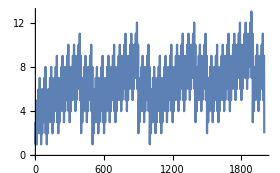
| Expected output: |  
  | -Graphics- |

Genere una cadena uniendo los números romanos de los números del 1 al 100. »

| Expected output: |  
  | "IIIIIIIVVVIVIIVIIIIXXXIXIIXIIIXIVXVXVIXVIIXVIIIXIXXXXXIXXIIXXIIIXXIVXXVXXVIXXVIIXXVIIIXXIXXXXXXXIXXXIIXXXIIIXXXIVXXXVXXXVIXXXVIIXXXVIIIXXXIXXLXLIXLIIXLIIIXLIVXLVXLVIXLVIIXLVIIIXLIXLLILIILIIILIVLVLVILVIILVIIILIXLXLXILXIILXIIILXIVLXVLXVILXVIILXVIIILXIXLXXLXXILXXIILXXIIILXXIVLXXVLXXVILXXVIILXXVIIILXXIXLXXXLXXXILXXXIILXXXIIILXXXIVLXXXVLXXXVILXXXVIILXXXVIIILXXXIXXCXCIXCIIXCIIIXCIVXCVXCVIXCVIIXCVIIIXCIXC" |

Cree una gráfica unida con los números de letra sucesivos para la concatenación de todos los números romanos del 1 al 30. »

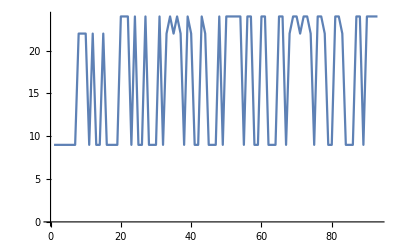
| Expected output: |  
  | -Graphics- |

Encuentre la máxima longitud de cadena de los nombres de los enteros del 1 al 1000. »

| Expected output: |  
  | 27 |

Haga una lista de mayúsculas de tamaño 20 con las letras del alfabeto, coloreadas aleatoriamente. »

| Expected output: |  
  | {"A","B","C","D","E","F","G","H","I","J","K","L","M","N","O","P","Q","R","S","T","U","V","W","X","Y","Z"} |

Haga una lista de 100 cadenas de 5 letras al azar tomadas del alfabeto ruso. »

| Expected output: |  
  | {"щёярф","цруйл","пхёкц","вгхфв","флэшм","яёуйу","лчтло","гнхшу","клчщч","эйарэ","совэф","цхшни","кдпфз","здъжь","ыйряп","змгщд","яфтбм","каоеэ","лкжрб","уатоо","нзквк","сонль","юфщзс","ябгшш","нясзо","хоэсв","псикх","днэхх","ъбшнщ","вюадг","ъчизб","цпвюа","ныиья","пгбби","ыхжзй","хвзет","чивир","чзгвм","млчюн","шгшнж","снслж","жйзьа","вйрак","вжънх","иёжщи","кшъиф","йцюую","цизшз","юшеях","хещэб","ффвмв","юяяко","лчвля","фцаьс","чрхиь","пунзщ","резуя","мпущд","гызшг","кёжмэ","бзяёя","хдхдъ","юзфща","ызуцр","ьяящл","оэмщи","эгщов","уфпвл","ядьщэ","йуэёэ","цснск","йпцжъ","йгухл","урмщр","щгхоф","ащвфх","кчьаь","улчпу","асмлж","какхй","рврвг","олйзя","ёцшцэ","энсав","еёяуб","чцеяс","вшэеи","чомры","ипбьэ","ьяфым","шидяб","щаюкы","шобро","айэнй","ашфгк","съгрм","ыфафщ","пбянс","фмсгф","хрубё"} |

Cree un Manipulate para mostrar los bordes de la letra A en tamaño 200, con niveles de difuminación del 0 al 50. »

| Expected output: |  
  |  |

Sume las letras A y B en blanco sobre negro, en tamaño 200. »

| Expected output: |  
  | -Graphics- |

Preguntas y respuestas

¿Qué diferencia hay entre "x" y  x?

"x" es una cadena; x es un símbolo de Wolfram Language, tal como Plus o Max, que puede definirse para llevar a cabo operaciones de cómputo. Más adelante se tocará este tema con toda amplitud.

¿Cómo se ingresan caracteres que no aparezcan en el teclado?

Puede usarse cualquier método que ofrezca el equipo que se use, o directamente con Wolfram Language usando constructos como \[Alpha].

¿Cómo se ponen las comillas (") dentro de una cadena?

Se usa \" (y si acaso se quiere poner literalmente \" en la cadena, póngase así: \\\"). (Habrá que usar muchas diagonales invertidas si se quiere escribir \\\": \\\\\\\".)

¿Cómo se determinan los colores en las nubes de palabras?

Por defecto, se hace aleatoriamente con una determinada paleta de color. Puede también fijarlo el usuario, si así lo desea.

¿A qué se debe que la nube de palabras muestre “s” como la letra más común?

Porque es la letra inicial más frecuente en las palabras comunes del inglés. Pero si se busca entre todas las letras, la más frecuente es la “e”.

¿Qué pasa con aquellas letras que no pertenecen al inglés? ¿Cómo se numeran?

LetterNumber["α","Greek"] da la numeración en el alfabeto griego. Todos los caracteres tienen asignado un código de carácter, que se puede obtener usando ToCharacterCode.

¿Qué alfabetos conoce Wolfram Language?

En principio, todos los que están en uso en la actualidad. Puede probarse con “Greek” o “Arabic”, o con el nombre de alguna otra lengua. Tómese en cuenta que cuando se usan caracteres acentuados en una lengua, a veces es complicado decidir si algo pertenece al alfabeto o si es simplemente un derivado.

¿Se pueden traducir palabras en vez de simplemente transliterar sus letras?

Sí. Use WordTranslation. Vea la Sección 35.

¿Se puede obtener listas de palabras comunes en lenguas diferentes del inglés?

Sí. Use WordList[Language→"Spanish"], etc.

Notas técnicas

RandomWord[10] responde con 10 palabras al azar. ¿Cuántas de ellas conoce el lector?

StringTake["string",-2] toma 2 caracteres contando desde el final de la cadena.

Cualquier carácter, ya sea “a”, “α” o “狼”, está representado por un código para carácter, que se encuentra con ToCharacterCode. Puede explorarse el “espacio Unicode” con FromCharacterCode.

Si se obtiene un resultado diferente del esperado al usar WikipediaData, se debe a que Wikipedia ha sufrido alguna modificación.

WordCloud elimina automáticamente palabras “no interesantes” del texto, tales como “el”, “y”, etc.

Si no se puede dar con el nombre de algún alfabeto o lenguaje, use ctrl= (como se describe en la Sección 16) para digitarlo en lenguaje natural.

Para explorar más

Guía para manipulación de cadenas de caracteres en Wolfram Language »